```mathematica
sars={{DateObject[{2003,3,17}],167,4},{DateObject[{2003,3,18}],219,4},{DateObject[{2003,3,19}],264,9},{DateObject[{2003,3,20}],306,10},{DateObject[{2003,3,21}],350,10},{DateObject[{2003,3,22}],386,11},{DateObject[{2003,3,24}],456,17},{DateObject[{2003,3,25}],487,17},{DateObject[{2003,3,26}],1323,49},{DateObject[{2003,3,27}],1408,53},{DateObject[{2003,3,28}],1485,53},{DateObject[{2003,3,29}],1550,54},{DateObject[{2003,3,31}],1622,58},
{DateObject[{2003,4,1}],1804,62},{DateObject[{2003,4,2}],2223,78},{DateObject[{2003,4,3}],2270,79},{DateObject[{2003,4,4}],2353,84},{DateObject[{2003,4,5}],2416,89},{DateObject[{2003,4,7}],2601,98},{DateObject[{2003,4,8}],2671,103},{DateObject[{2003,4,9}],2722,106},{DateObject[{2003,4,10}],2781,111},{DateObject[{2003,4,11}],2890,116},{DateObject[{2003,4,12}],2960,119},{DateObject[{2003,4,14}],3169,144},{DateObject[{2003,4,15}],3235,154},{DateObject[{2003,4,16}],3293,159},{DateObject[{2003,4,17}],3389,165},{DateObject[{2003,4,18}],3547,182},{DateObject[{2003,4,20}],3547,182},{DateObject[{2003,4,21}],3861,217},{DateObject[{2003,4,22}],3947,229},{DateObject[{2003,4,23}],4288,251},{DateObject[{2003,4,24}],4439,263},{DateObject[{2003,4,25}],4649,274},{DateObject[{2003,4,26}],4836,293},{DateObject[{2003,4,28}],5050,321},{DateObject[{2003,4,29}],5462,353},{DateObject[{2003,4,30}],5663,372},
{DateObject[{2003,5,1}],5865,391},{DateObject[{2003,5,2}],6054,417},{DateObject[{2003,5,3}],6234,435},{DateObject[{2003,5,5}],6583,461},{DateObject[{2003,5,6}],6727,478},{DateObject[{2003,5,7}],6903,495},{DateObject[{2003,5,8}],7053,506},{DateObject[{2003,5,9}],7183,514},{DateObject[{2003,5,10}],7296,526},{DateObject[{2003,5,12}],7447,552},{DateObject[{2003,5,13}],7548,573},{DateObject[{2003,5,14}],7628,587},{DateObject[{2003,5,15}],7699,598},{DateObject[{2003,5,16}],7739,611},{DateObject[{2003,5,17}],7761,623},{DateObject[{2003,5,19}],7864,643},{DateObject[{2003,5,20}],7919,662},{DateObject[{2003,5,21}],7956,666},{DateObject[{2003,5,22}],8046,682},{DateObject[{2003,5,23}],8117,689},{DateObject[{2003,5,24}],8141,696},{DateObject[{2003,5,26}],8202,725},{DateObject[{2003,5,27}],8221,735},{DateObject[{2003,5,28}],8240,745},{DateObject[{2003,5,29}],8295,750},{DateObject[{2003,5,30}],8317,754},{DateObject[{2003,5,31}],8360,764},
{DateObject[{2003,6,2}],8384,770},{DateObject[{2003,6,3}],8398,772},{DateObject[{2003,6,4}],8402,772},{DateObject[{2003,6,5}],8403,775},{DateObject[{2003,6,6}],8404,779},{DateObject[{2003,6,9}],8421,784},{DateObject[{2003,6,10}],8430,789},{DateObject[{2003,6,11}],8435,789},{DateObject[{2003,6,12}],8445,790},{DateObject[{2003,6,13}],8454,792},{DateObject[{2003,6,16}],8460,799},{DateObject[{2003,6,17}],8464,799},{DateObject[{2003,6,18}],8465,801},{DateObject[{2003,6,20}],8462,804},{DateObject[{2003,6,20}],8461,804},{DateObject[{2003,6,23}],8459,805},{DateObject[{2003,6,24}],8458,807},{DateObject[{2003,6,25}],8460,808},{DateObject[{2003,6,26}],8456,809},{DateObject[{2003,6,27}],8450,810},{DateObject[{2003,6,30}],8447,811},
{DateObject[{2003,7,1}],8445,812},{DateObject[{2003,7,2}],8442,812},{DateObject[{2003,7,3}],8439,812},{DateObject[{2003,7,4}],8439,812},{DateObject[{2003,7,7}],8439,812},{DateObject[{2003,7,8}],8436,812},{DateObject[{2003,7,9}],8436,812},{DateObject[{2003,7,10}],8437,812},{DateObject[{2003,7,11}],8437,813}};
```

```mathematica
ncov={{DateObject[{2020,1,20}],282,6},{DateObject[{2020,1,21}],314,6},{DateObject[{2020,1,23}],581,17},{DateObject[{2020,1,24}],846,25},{DateObject[{2020,1,25}],1320,41},{DateObject[{2020,1,26}],2014,42},{DateObject[{2020,1,27}],2798,80},{DateObject[{2020,1,28}],4593,106},{DateObject[{2020,1,29}],6065,132},{DateObject[{2020,1,30}],7818,170},{DateObject[{2020,1,31}],9826,213}};
```

```mathematica
sarscases=Table[{sars[[i,1]]-DateObject[{2003,3,17}],sars[[i,2]]},{i,1,Length[sars]}];
ncovcases=Table[{ncov[[i,1]]-DateObject[{2020,1,20}],ncov[[i,2]]},{i,1,Length[ncov]}];
sarsdeaths=Table[{sars[[i,1]]-DateObject[{2003,3,17}],sars[[i,3]]},{i,1,Length[sars]}];
ncovdeaths=Table[{ncov[[i,1]]-DateObject[{2020,1,20}],ncov[[i,3]]},{i,1,Length[ncov]}];
```

```mathematica
(*ncov sequenced 1/13
sars sequenced 4/14 *)
```

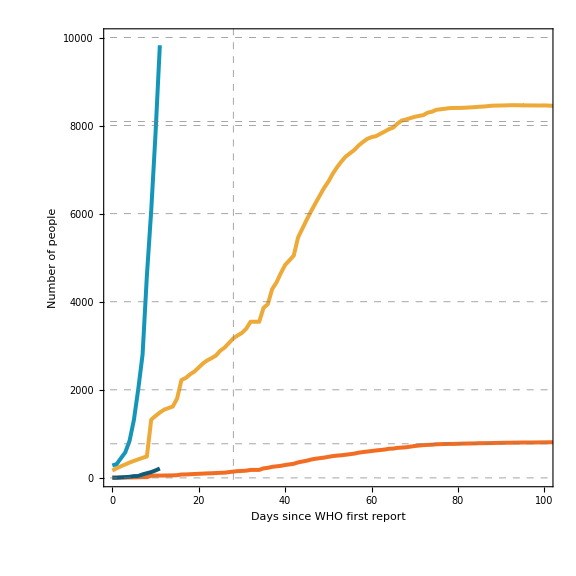

```mathematica
ListPlot[{sarscases,ncovcases,sarsdeaths,ncovdeaths},PlotRange->{{0,100},{0,10000}},Joined->True,InterpolationOrder->1,Frame->{True,True,False,False},GridLines->{{28}, {4000,2000,6000,8000,8096,774,10000,0}},AspectRatio->1,GridLinesStyle->Directive[Gray,Thin,Dashed],PlotStyle->{Directive[color8Amber,Thickness[0.005]],Directive[color4Alice,Thickness[0.005]],Directive[color10Carol,Thickness[0.005]],Directive[color2Sophia,Thickness[0.005]]},LabelStyle->{FontFamily->"Mada",20},FrameLabel->{"Days since WHO first report","Number of people"},PlotLegends->{"","","",""},ImageSize->Large,FrameTicks->{{{2000,4000,6000,8000,10000,0},None},{{0,20,40,60,80,100},None}}]
```